# ci基盤ログの解析:推定ユーザーごとのアクセス推移（ユーザーストーリー）

-Graphics-

生ログ

## 準備

```mathematica
start=AbsoluteTime[Date[]]
```

3.910267442521283×10^9

#### 変数

```mathematica
date="20231120"
```

20231120

```mathematica
mountdir="/Volumes/home/NII/togo-log/rcoslogs/"
```

/Volumes/home/NII/togo-log/rcoslogs/

```mathematica
vocdir=mountdir<>"voc"
```

/Volumes/home/NII/togo-log/rcoslogs/voc

```mathematica
case={"ci","cs","la","wk"}
```

{ci,cs,la,wk}

```mathematica
base["ci"]="T=ci"
base["cs"]="T=cs"
base["la"]="T=la"
base["wk"]="T=wk"
base["all"]="T=4"
```

T=ci

T=cs

T=la

T=wk

T=4

#### 解析用データ

```mathematica
fileliststr=Import[mountdir<>"log/D="<>date<>"/"<>"filenames","String"]
```

log-20231120.rcoslog0003.log

```mathematica
filelist=StringSplit[fileliststr]
```

{log-20231120.rcoslog0003.log}

元ログの大きさ （wc）

```mathematica
logwc=Import[mountdir<>"log/D="<>date<>"/logfiles.wc","String"]
```

22645372 320069013 10381193889 log-20231120.rcoslog0003.log

```mathematica
ckanfile=mountdir<>"crid/CIRDEV-1067_crid_list/ckan_product_crid_list.txt"
```

/Volumes/home/NII/togo-log/rcoslogs/crid/CIRDEV-1067_crid_list/ckan_product_crid_list.txt

```mathematica
ckanSt=Import[ckanfile,"String"];
```

```mathematica
(ckanName=StringSplit[ckanSt,"\n"])//Dimensions
```

{92643}

```mathematica
(ckanCridAC=Apply[Association,Map[#->#&,ckanName]])//Dimensions
```

{92643}

#### プログラム

vertexを指定してdirected-edgeを辿る部分グラフ抽出の関数：

```mathematica
directedConnectedGraphComponent[g_,v_]:=Module[{vAll,vOther,addEdge},
vAll=VertexList[g];
vOther=Complement[vAll,{v}];
addEdge=Map[#->v&,vOther];
Subgraph[g,ConnectedComponents[Flatten[{EdgeList[g],addEdge},1],v][[1]]]
]
```

グラフよりinがないノードを検出してそこから(g,v)に対して上記関数をアプライする関数：

```mathematica
vertexInGraph[g_Graph]:=Module[{deg,pos,vname},
deg=VertexInDegree[g];
pos=Position[deg,0]//Flatten//Union;
vname=VertexList[g][[pos]];
Map[directedConnectedGraphComponent[g,#]&,vname]
]
vertexInGraph[g_Integer]:=g
```

story-group-indexを各グラフにdistributeする関数：

```mathematica
distributeIdxGr[idxGr_]:=Module[
{date,idx,gr},
date=idxGr[[1]];
idx=idxGr[[2]];
gr=idxGr[[3]];
Map[{date,idx,#}&,gr]
]
```

stringからfqdnのみ抽出する関数：

```mathematica
fqdnFromPath[s_]:=StringJoin[StringSplit[s,"/"]⟦{1,3}⟧]
```

```mathematica
fqdnFromGraph[g_Graph]:=Union[Sort[Map[fqdnFromPath,VertexList[g]]]]
```

## Data (4)

### データ(ci)

```mathematica
dir["ci"]=mountdir<>"log/D="<>date<>"/"<>base["ci"]
```

/Volumes/home/NII/togo-log/rcoslogs/log/D=20231120/T=ci

#### データの読み込み

```mathematica
file["ci"]="self.1"
```

self.1

```mathematica
str["ci"]=Import[dir["ci"]<>"/"<>file["ci"],"String"];
```

```mathematica
(strSplt["ci"]=StringSplit[str["ci"],"\n"])//Length
```

2557038

```mathematica
(strSplt1["ci"]=Map[StringSplit[#,"\t"]&,strSplt["ci"]])//Dimensions
```

{2557038,15}

#### カラムポジションの調整

不要。

#### 各値の補完

パスのキーを削除しURLを補完する。

```mathematica
strSplt1C["ci"]=Map[ReplacePart[#,8->"https://cir.nii.ac.jp/"<>StringDrop[#[[8]],8]]&,strSplt1["ci"]];
```

レファラーのキーを削除する。

```mathematica
strSplt1CC["ci"]=Map[ReplacePart[#,11->StringDrop[#[[11]],10]]&,strSplt1C["ci"]];
```

時刻をMathematica標準にする。

ログのdateをWLの時間表現に変換する関数

```mathematica
logdateToTime["ci"][s_String]:=AbsoluteTime[DateList[StringTake[s,{8,-6}]]]
```

```mathematica
logdateToTime["ci"][strSplt1CC["ci"][[1]][[6]]]
```

3.90943×10^9

```mathematica
strSplt1CCC["ci"]=Map[ReplacePart[#,6->logdateToTime["ci"][#[[6]]]]&,strSplt1CC["ci"]];
```

remoteをアドレスのみに。

```mathematica
ip["ci"][str_]:=StringSplit[str,"\":\""][[2]]
```

```mathematica
strSplt1CCCCpre["ci"]=Map[ReplacePart[#,3->ip["ci"][#[[3]]]]&,strSplt1CCC["ci"]];
```

```mathematica
strSplt1CCCCpre["ci"][[10]]//TableForm
```

2023-11-19T15:00:01Z
log.ci0001.aws.wa03.yobi
35.216.53.137
host":"-
user":"-
3.90943×10^9
method":"GET
https://cir.nii.ac.jp/all?q=%E4%BA%95%E4%B8%8A%E5%93%B2%E6%AC%A1%E9%83%8E
code":"200
size":"17876
https://cir.nii.ac.jp/crid/1020282257445677312
agent":"Mozilla/5.0 (Windows NT 10.0; Win64; x64) AppleWebKit/537.36 (KHTML, like Gecko) Chrome/119.0.0.0 Safari/537.36
http_x_forwarded_for":"\"35.216.53.137\"
request_time":"0.229
upstream_response_time":"0.229"}

pathのCRID、refererのCRIDを追加。

```mathematica
toCRID[s_String/;StringMatchQ[s,RegularExpression["https://cir.nii.ac.jp/crid/.*"]]]:=StringTake[StringSplit[s,"/"][[5]],19]
```

```mathematica
strSplt1CCCC["ci"]=Map[Join[#,{toCRID[#[[8]]],toCRID[#[[11]]]}]&,strSplt1CCCCpre["ci"]];
```

StringTake::take: Cannot take positions 1 through 19 in "wp-login.php".

StringTake::take: Cannot take positions 1 through 19 in "ajax-loader.gif".

StringTake::take: Cannot take positions 1 through 19 in "wp-login.php".

General::stop: Further output of StringTake::take will be suppressed during this calculation.

Part::partw: Part 5 of {https:,,cir.nii.ac.jp,crid} does not exist.

StringTake::strse: String or list of strings expected at position 1 in StringTake[{https:,,cir.nii.ac.jp,crid}⟦5⟧,19].

Part::partw: Part 5 of {https:,,cir.nii.ac.jp,crid} does not exist.

StringTake::strse: String or list of strings expected at position 1 in StringTake[{https:,,cir.nii.ac.jp,crid}⟦5⟧,19].

Part::partw: Part 5 of {https:,,cir.nii.ac.jp,crid} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

StringTake::strse: String or list of strings expected at position 1 in StringTake[{https:,,cir.nii.ac.jp,crid}⟦5⟧,19].

General::stop: Further output of StringTake::strse will be suppressed during this calculation.

```mathematica
strSplt1CCCC["ci"][[8]]//TableForm
```

2023-11-19T15:00:01Z
log.ci0001.aws.wa03.yobi
66.249.71.32
host":"-
user":"-
3.90943×10^9
method":"GET
https://cir.nii.ac.jp/crid/1361981470279206912
code":"200
size":"13350
-
agent":"Mozilla/5.0 (compatible; Googlebot/2.1; +http://www.google.com/bot.html)
http_x_forwarded_for":"\"66.249.71.32\"
request_time":"0.032
upstream_response_time":"0.032"}
1361981470279206912
toCRID[-]

```mathematica
accessTime["ci"]=Map[#[[6]]&,strSplt1CCCC["ci"]];
```

## リンク(ci)

```mathematica
Timing[(strSplt1CCCC["ci"]=SortBy[strSplt1CCCC["ci"],{#[[3]],#[[12]],#[[6]]}&])//Dimensions]
```

{30.7694,{2557038,17}}

抽出ログの行インデックスをアペンド

```mathematica
apIdx["ci"]=Table[i,{i,Length[strSplt1CCCC["ci"]]}];
```

```mathematica
idxLog["ci"]=Map[Append[#[[1]],#[[2]]]&,Transpose[{strSplt1CCCC["ci"],apIdx["ci"]}]];
```

```mathematica
idxLog["ci"][[1]]//TableForm
```

2023-11-20T01:13:04Z
log.ci0001.aws.wa03.yobi
100.0.13.114
host":"-
user":"-
3.90946×10^9
method":"GET
https://cir.nii.ac.jp/crid/1130000794663951744
code":"200
size":"12741
https://scholar.google.com/scholar?as_sdt=0%2C22&btnG=&hl=en&inst=10716753698184193673&q=%22Children%20in%20Bosnian%20tragedy%22
agent":"Mozilla/5.0 (Macintosh; Intel Mac OS X 10_15_7) AppleWebKit/605.1.15 (KHTML, like Gecko) Version/17.0 Safari/605.1.15
http_x_forwarded_for":"\"100.0.13.114\"
request_time":"0.087
upstream_response_time":"0.087"}
1130000794663951744
toCRID[https://scholar.google.com/scholar?as_sdt=0%2C22&btnG=&hl=en&inst=10716753698184193673&q=%22Children%20in%20Bosnian%20tragedy%22]
1

### ckanデータの処理(ciのみ)

CKAN-CRIDの存在確認：

パス情報：

```mathematica
(ckanPathE["ci"]=Map[ckanCridAC[#[[-3]]]&,idxLog["ci"]])//Dimensions
```

{2557038}

```mathematica
(ckanCridPLogPos["ci"]=Flatten[Position[ckanPathE["ci"],_String,{1}]])//Length
```

188

```mathematica
(ckanCridPLogPosAC["ci"]=Association[Map[#->#&,ckanCridPLogPos["ci"]]])//Length
```

188

```mathematica
ckanCridPlist=Cases[ckanPathE["ci"],_String]
```

{1690013498967485824,1690294973953606144,1690857923910863488,1690576448919038976,1690576448920292608,1690857923906377472,1690013498975618304,1690013498964577920,1690013498964701696,1690013498968898432,1690013498976227968,1690013498976487936,1690013498979181312,1690013498969262976,1690857923911162496,1690857923911162496,1690576448922822016,1690013498972366720,1690857923910794368,1690857923907923840,1690294973953596416,1690294973942275072,1690857923906846848,1690294973943387392,1690857923906980992,1690013498970293760,1690857923900427008,1690857923900427008,1690013498966868608,1690576448934290304,1690013498976692096,1690857923908567808,1690857923900409472,1690857923900409472,1690857923900409472,1690857923900409472,1690576448930414208,1690576448930414208,1690013498981154560,1690294973948438272,1690857923902164352,1690576448920209408,1690013498970751360,1690013498970751360,1690857923906768768,1690857977695030656,1690013498965360000,1690013498973017728,1690576448927414784,1690294973946289152,1690294973954989568,1690294973952069632,1690013498966080640,1690013498980164608,1690013498976675840,1690576448930311040,1690013498981705728,1690576448931596416,1690294973957276416,1690294973957307904,1690013498980381824,1690576448930307584,1690013498977051904,1690013498977051904,1690294973956643712,1690857923896633856,1690294973952059392,1690013498977000064,1690857923906377472,1690857923906219648,1690013498969026688,1690294973942895232,1690857923910454272,1690013498969192960,1690857923906980992,1690013498970759936,1690013498968870400,1690013498968870400,1690013498965808896,1690013498980300544,1690013498980300544,1690013498967067008,1690013498981165184,1690857923896500608,1690294973953358208,1690013498976260096,1690294973944214016,1690294973957605248,1690576448929296896,1690013498980133376,1690013498968336512,1690013498969028992,1690294973957933952,1690294973957691904,1690013498970098176,1690013498966834944,1690013498969104384,1690013498969104384,1690013498980300544,1690857923906377472,1690294973957691904,1690013498966314880,1690857923901621504,1690013498980805248,1690576448929831808,1690857923903994368,1690013498979924864,1690576448918169728,1690013498965071744,1690013498966457984,1690294973957407104,1690013498980300544,1690294973947167488,1690013498967385472,1690857923900576640,1690857923900425984,1690013498965660416,1690857923897603712,1690013498966657152,1690576448923884288,1690013498972366720,1690294973944516352,1690857923905234048,1690576448932049536,1690013498965205376,1690294973947166848,1690576448918183040,1690294973942927360,1690013498977051904,1690857923906219648,1690294973953244288,1690294973945187712,1690013498974767872,1690013498973017728,1690013498973017728,1690294973942466432,1690294973942466432,1690294973948194560,1690294973956812416,1690013498971177472,1690013498972893952,1690013498977051904,1690013498980189056,1690294973947002624,1690576448924242816,1690013498980805248,1690013498977051904,1690576448928860032,1690576448933759744,1690013498981131520,1690294973947010816,1690576448930598656,1690857923906248832,1690013498976259200,1690294973947166848,1690013498977616512,1690294973946873856,1690576448929717248,1690857923903252352,1690013498976926208,1690857923906649088,1690576448929825024,1690576448922046720,1690294973943723008,1690294973947054464,1690294973952656256,1690013498980231936,1690294973947469568,1690576448928912256,1690013498968198784,1690294973953391872,1690576448918275456,1690013498976893568,1690294973946183680,1690857977695145728,1690294973947162368,1690857923900942976,1690857923911288192,1690857923894718208,1690013498966588672,1690294973956643712,1690576448934769792,1690576448921676032,1690857923897304192,1690294973950713344,1690857923898270720,1690013498980133376,1690857923906654976}

リファラー情報：

```mathematica
ckanRefE["ci"]=Map[ckanCridAC[#[[-2]]]&,idxLog["ci"]];
```

```mathematica
(ckanCridRLogPos["ci"]=Flatten[Position[ckanRefE["ci"],_String,{1}]])//Length
```

25

```mathematica
(ckanCridRLogPosAC["ci"]=Association[Map[#->#&,ckanCridRLogPos["ci"]]])//Length
```

25

```mathematica
ckanCridRlist=Cases[ckanRefE["ci"],_String]
```

{1690013498969262976,1690857923907923840,1690857923907923840,1690857923907923840,1690013498970293760,1690576448934290304,1690294973948438272,1690294973948438272,1690013498965360000,1690013498965360000,1690576448930307584,1690294973946873856,1690013498965808896,1690013498981165184,1690013498981165184,1690013498981165184,1690013498981165184,1690857923901621504,1690013498980300544,1690013498980300544,1690857923900576640,1690857923900576640,1690857923900576640,1690294973942466432,1690294973942466432}

パスとリファラーをマージ：

```mathematica
(ckanCridPRLogPos["ci"]=Union[ckanCridPLogPos["ci"],ckanCridRLogPos["ci"]])//Length
```

213

```mathematica
(ckanCridPRLogPosAC["ci"]=Association[Map[#->#&,ckanCridPRLogPos["ci"]]])//Length
```

213

```mathematica
ckanCridPRU=Union[ckanCridPlist,ckanCridRlist]
```

{1690013498964577920,1690013498964701696,1690013498965071744,1690013498965205376,1690013498965360000,1690013498965660416,1690013498965808896,1690013498966080640,1690013498966314880,1690013498966457984,1690013498966588672,1690013498966657152,1690013498966834944,1690013498966868608,1690013498967067008,1690013498967385472,1690013498967485824,1690013498968198784,1690013498968336512,1690013498968870400,1690013498968898432,1690013498969026688,1690013498969028992,1690013498969104384,1690013498969192960,1690013498969262976,1690013498970098176,1690013498970293760,1690013498970751360,1690013498970759936,1690013498971177472,1690013498972366720,1690013498972893952,1690013498973017728,1690013498974767872,1690013498975618304,1690013498976227968,1690013498976259200,1690013498976260096,1690013498976487936,1690013498976675840,1690013498976692096,1690013498976893568,1690013498976926208,1690013498977000064,1690013498977051904,1690013498977616512,1690013498979181312,1690013498979924864,1690013498980133376,1690013498980164608,1690013498980189056,1690013498980231936,1690013498980300544,1690013498980381824,1690013498980805248,1690013498981131520,1690013498981154560,1690013498981165184,1690013498981705728,1690294973942275072,1690294973942466432,1690294973942895232,1690294973942927360,1690294973943387392,1690294973943723008,1690294973944214016,1690294973944516352,1690294973945187712,1690294973946183680,1690294973946289152,1690294973946873856,1690294973947002624,1690294973947010816,1690294973947054464,1690294973947162368,1690294973947166848,1690294973947167488,1690294973947469568,1690294973948194560,1690294973948438272,1690294973950713344,1690294973952059392,1690294973952069632,1690294973952656256,1690294973953244288,1690294973953358208,1690294973953391872,1690294973953596416,1690294973953606144,1690294973954989568,1690294973956643712,1690294973956812416,1690294973957276416,1690294973957307904,1690294973957407104,1690294973957605248,1690294973957691904,1690294973957933952,1690576448918169728,1690576448918183040,1690576448918275456,1690576448919038976,1690576448920209408,1690576448920292608,1690576448921676032,1690576448922046720,1690576448922822016,1690576448923884288,1690576448924242816,1690576448927414784,1690576448928860032,1690576448928912256,1690576448929296896,1690576448929717248,1690576448929825024,1690576448929831808,1690576448930307584,1690576448930311040,1690576448930414208,1690576448930598656,1690576448931596416,1690576448932049536,1690576448933759744,1690576448934290304,1690576448934769792,1690857923894718208,1690857923896500608,1690857923896633856,1690857923897304192,1690857923897603712,1690857923898270720,1690857923900409472,1690857923900425984,1690857923900427008,1690857923900576640,1690857923900942976,1690857923901621504,1690857923902164352,1690857923903252352,1690857923903994368,1690857923905234048,1690857923906219648,1690857923906248832,1690857923906377472,1690857923906649088,1690857923906654976,1690857923906768768,1690857923906846848,1690857923906980992,1690857923907923840,1690857923908567808,1690857923910454272,1690857923910794368,1690857923910863488,1690857923911162496,1690857923911288192,1690857977695030656,1690857977695145728}

```mathematica
ckanCridPRACQ=Association[Map[#->True&,ckanCridPRU]]
```

<|1690013498964577920→True,1690013498964701696→True,1690013498965071744→True,1690013498965205376→True,1690013498965360000→True,1690013498965660416→True,1690013498965808896→True,1690013498966080640→True,1690013498966314880→True,1690013498966457984→True,1690013498966588672→True,1690013498966657152→True,1690013498966834944→True,1690013498966868608→True,1690013498967067008→True,1690013498967385472→True,1690013498967485824→True,1690013498968198784→True,1690013498968336512→True,1690013498968870400→True,1690013498968898432→True,1690013498969026688→True,1690013498969028992→True,1690013498969104384→True,1690013498969192960→True,1690013498969262976→True,1690013498970098176→True,1690013498970293760→True,1690013498970751360→True,1690013498970759936→True,1690013498971177472→True,1690013498972366720→True,1690013498972893952→True,1690013498973017728→True,1690013498974767872→True,1690013498975618304→True,1690013498976227968→True,1690013498976259200→True,1690013498976260096→True,1690013498976487936→True,1690013498976675840→True,1690013498976692096→True,1690013498976893568→True,1690013498976926208→True,1690013498977000064→True,1690013498977051904→True,1690013498977616512→True,1690013498979181312→True,1690013498979924864→True,1690013498980133376→True,1690013498980164608→True,1690013498980189056→True,1690013498980231936→True,1690013498980300544→True,1690013498980381824→True,1690013498980805248→True,1690013498981131520→True,1690013498981154560→True,1690013498981165184→True,1690013498981705728→True,1690294973942275072→True,1690294973942466432→True,1690294973942895232→True,1690294973942927360→True,1690294973943387392→True,1690294973943723008→True,1690294973944214016→True,1690294973944516352→True,1690294973945187712→True,1690294973946183680→True,1690294973946289152→True,1690294973946873856→True,1690294973947002624→True,1690294973947010816→True,1690294973947054464→True,1690294973947162368→True,1690294973947166848→True,1690294973947167488→True,1690294973947469568→True,1690294973948194560→True,1690294973948438272→True,1690294973950713344→True,1690294973952059392→True,1690294973952069632→True,1690294973952656256→True,1690294973953244288→True,1690294973953358208→True,1690294973953391872→True,1690294973953596416→True,1690294973953606144→True,1690294973954989568→True,1690294973956643712→True,1690294973956812416→True,1690294973957276416→True,1690294973957307904→True,1690294973957407104→True,1690294973957605248→True,1690294973957691904→True,1690294973957933952→True,1690576448918169728→True,1690576448918183040→True,1690576448918275456→True,1690576448919038976→True,1690576448920209408→True,1690576448920292608→True,1690576448921676032→True,1690576448922046720→True,1690576448922822016→True,1690576448923884288→True,1690576448924242816→True,1690576448927414784→True,1690576448928860032→True,1690576448928912256→True,1690576448929296896→True,1690576448929717248→True,1690576448929825024→True,1690576448929831808→True,1690576448930307584→True,1690576448930311040→True,1690576448930414208→True,1690576448930598656→True,1690576448931596416→True,1690576448932049536→True,1690576448933759744→True,1690576448934290304→True,1690576448934769792→True,1690857923894718208→True,1690857923896500608→True,1690857923896633856→True,1690857923897304192→True,1690857923897603712→True,1690857923898270720→True,1690857923900409472→True,1690857923900425984→True,1690857923900427008→True,1690857923900576640→True,1690857923900942976→True,1690857923901621504→True,1690857923902164352→True,1690857923903252352→True,1690857923903994368→True,1690857923905234048→True,1690857923906219648→True,1690857923906248832→True,1690857923906377472→True,1690857923906649088→True,1690857923906654976→True,1690857923906768768→True,1690857923906846848→True,1690857923906980992→True,1690857923907923840→True,1690857923908567808→True,1690857923910454272→True,1690857923910794368→True,1690857923910863488→True,1690857923911162496→True,1690857923911288192→True,1690857977695030656→True,1690857977695145728→True|>

## ユーザー生成(ci)

各条件のキーを策定：

3項のソースアドレス

12項のユーザーエージェント

6項のアクセス時刻

まず推定ユーザーごとにgathgerする。

#### ユーザー生成

ソースアドレスとユーザーエージェントをキーにしてsplitする。

```mathematica
((idxLogS["ci"]=Split[idxLog["ci"],#1[[3]]==#2[[3]]&&#1[[12]]==#2[[12]]&])//Length)
```

162800

```mathematica
idxLogLen["ci"]=Length[idxLog["ci"]]
```

2557038

上記の数が推定ユーザー数。

## グラフ生成(4):inf

#### Pre Op 1

ストーリー分割：

時間設定をinfにすることによりアクセス時間では分割しない。
1. ユーザーごとに分割 -> userGr,userGrIdx
2. 繋がらないエッジで分割 -> user2GrIdx
3. 上記の各グラフより in がないVertexを起点としてoutで辿れるパスにより各サブグラフを抽出 -> storyGrIdx
　のちに扱いやすい構造にする。

0. 時間で分割しない -> 全てを要素1のリストにする：

```mathematica
Timing[(idxLogSinf["ci"]=Map[Split[#,#2[[6]]-#1[[6]]<=Infinity&]&,idxLogS["ci"]])//Dimensions]
```

{4.96807,{162800,1}}

```mathematica
idxLogS[4][[1]]
```

4

ユーザーストーリーグループに対応するログを参照する関数：

```mathematica
refstglog["ci"][g_]:={g[[1]],g[[3]],Part[idxLogSinf["ci"],g[[2,1]],g[[2,2]]]}
```

#### Pre Op 2.1

Saveデータがある時は読み込む：

#### Pre Op 2.2

<<< Saveデータを読んだ時はここから飛ばす。 >>>

1. ユーザーごとのグラフ生成：

エッジルール作成（この時点でエッジ以外の情報が落ちる、アクセス時刻とログ行インデックスをエッジに設定する）：

```mathematica
userGrER["ci"]=Map[Map[DirectedEdge[#[[11]],#[[8]],{#[[6]],#[[-1]]}]&,#]&,idxLogSinf["ci"],{2}];
```

```mathematica
userGrER["ci"][[2]]
```

{{https://scholar.google.com/https://cir.nii.ac.jp/crid/1130282272421828992{3.90944×10^9,2}}}

```mathematica
(userGr["ci"]=Map[Graph[#,VertexLabels->Automatic]&,userGrER["ci"],{2}])//Length
```

162800

上記がユーザー数。

ここでindexを作成。{date,{userID, log-groupID}, G} とする。

```mathematica
userGrIdx["ci"]=MapIndexed[{date,#2,#1}&,userGr["ci"],{2}];
```

2. ユーザーごとのグラフをさらにエッジでつながらない部分グラフに分ける：

```mathematica
Timing[(user2GrIdx["ci"]=Map[{#[[1]],#[[2]],WeaklyConnectedGraphComponents[#[[3]]]}&,userGrIdx["ci"],{2}])//Dimensions]
```

{172.598,{162800,1,3}}

3. 分けられた各グラフをさらにinがないノードをスタートとするグラフに分ける：

```mathematica
Timing[(storyGrIdx["ci"]=Map[vertexInGraph,user2GrIdx["ci"],{4}])//Dimensions ]
```

{204.356,{162800,1,3}}

扱いやすい構造にする。-> storyGrIdxFlDs[4]

グラフリストをflatten:

```mathematica
(storyGrIdxFl["ci"]=Map[{#[[1]],#[[2]],Flatten[#[[3]]]}&,Flatten[storyGrIdx["ci"],1]])//Dimensions
```

{162800,3}

```mathematica
storyGrIdxFl["ci"][[1]][[3]][[1]]//EdgeList
```

{https://scholar.google.com/scholar?as_sdt=0%2C22&btnG=&hl=en&inst=10716753698184193673&q=%22Children%20in%20Bosnian%20tragedy%22https://cir.nii.ac.jp/crid/1130000794663951744{3.90946×10^9,1}}

各グラフに{userID, story-groupID}をdistribute:

```mathematica
(storyGrIdxFlDs["ci"]=Flatten[Map[distributeIdxGr,storyGrIdxFl["ci"]],1])//Dimensions
```

{223894,3}

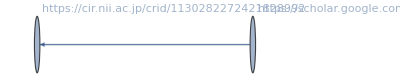
{20231120,{2,1},-Graphics-}

```mathematica
storyGrIdxFlDs["ci"][[2]]
```

4. 不要と思われるvertexを削除(1)：

```mathematica
(storyGrIdxFlDsVD1["ci"]=Map[{#[[1]],#[[2]],If[VertexQ[#[[3]],"-"],VertexDelete[#[[3]],"-"],#[[3]]]}&,storyGrIdxFlDs["ci"]])//Dimensions
```

{223894,3}

5. 不要と思われるvertexを削除(2)：

rm候補のパターン：

```mathematica
rmpattAll[4]={rmpatt[4][1]=RegularExpression["https://jupyter.cs.rcos.nii.ac.jp/hub/static.*"],
rmpatt[4][2]=RegularExpression["https://jdcat.jsps.go.jp/api.*"],
rmpatt[4][3]=RegularExpression["https://jupyter.cs.rcos.nii.ac.jp/hub/.*api.*"],
rmpatt[4][4]=RegularExpression["https://jupyter.cs.rcos.nii.ac.jp/user/.*/api.*"],
rmpatt[4][5]=RegularExpression["https://jupyter.cs.rcos.nii.ac.jp/img.*"],
rmpatt[4][6]=RegularExpression["https://.*/.*\\.svg"],
rmpatt[4][7]=RegularExpression["https://.*/.*\\.js"],
rmpatt[4][8]=RegularExpression["https://jupyter.cs.rcos.nii.ac.jp/.*\\.js\\?.*"],
rmpatt[4][9]=RegularExpression["https://jdcat.jsps.go.jp/.*\\.js\\?.*"],
rmpatt[4][10]=RegularExpression["https://.*/.*\\.woff2.*"],
rmpatt[4][11]=RegularExpression["https://.*/.*\\.css"],
rmpatt[4][12]=RegularExpression["https://.*/css/.*"],
rmpatt[4][13]=RegularExpression["https://.*/.*\\.favicon.ico"],
rmpatt[4][14]="https://jdcat.jsps.go.jp/get_search_setting",
rmpatt[4][15]="https://jdcat.jsps.go.jp/facet-search/get-title-and-order"
};
```

rm候補のパターンから削除頂点リストを生成（参考）：

```mathematica
createRmList[gr_,rmpatt_]:=Module[{vlist},
vlist=VertexList[gr];
Union[Flatten[Table[Cases[vlist,x_/;StringMatchQ[x,rmpatt[[n]]]],{n,Length[rmpatt]}]]]
]
```

rm候補のパターンを指定してグラフからマッチする頂点を削除する関数：

```mathematica
rmV[gr_,rmpatt_]:=Module[{vlist,pathlist},
vlist=VertexList[gr];
pathlist=Union[Flatten[Table[Cases[vlist,x_/;StringMatchQ[x,rmpatt[[n]]]],{n,Length[rmpatt]}]]];
VertexDelete[gr,pathlist]
]
```

```mathematica
(storyGrIdxFlDsVD2["ci"]=Map[{#[[1]],#[[2]],rmV[#[[3]],rmpattAll[4]]}&,storyGrIdxFlDsVD1["ci"]])//Dimensions
```

{223894,3}

6. 以上の操作により不正となったグラフを削除(対象をpick)：

ノード数 >= 2：

```mathematica
pickPos["ci"][1]=Flatten[Position[Map[VertexCount[#[[3]]]&,storyGrIdxFlDsVD2["ci"]],x_/;x>=2]];
```

```mathematica
(storyGrIdxFlDs2["ci"]=storyGrIdxFlDsVD2["ci"][[pickPos["ci"][1]]])//Dimensions
```

{198671,3}

エッジ数 >= 1：

```mathematica
pickPos["ci"][2]=Flatten[Position[Map[EdgeCount[#[[3]]]&,storyGrIdxFlDs2["ci"]],x_/;x>=1]];
```

```mathematica
(storyGrIdxFlDs3["ci"]=storyGrIdxFlDs2["ci"][[pickPos["ci"][2]]])//Dimensions
```

{185893,3}

上が分離されたストーリー

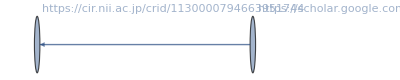
{20231120,{1,1},-Graphics-}

```mathematica
storyGrIdxFlDs3["ci"][[1]]
```

#### Pre Op 2.2.1 : save

```mathematica
savedir=mountdir<>"log/D="<>date<>"/"<>base["ci"]
```

/Volumes/home/NII/togo-log/rcoslogs/log/D=20231120/T=ci

```mathematica
SetDirectory[savedir]
```

/Volumes/home/NII/togo-log/rcoslogs/log/D=20231120/T=ci

```mathematica
Directory[]
```

/Volumes/home/NII/togo-log/rcoslogs/log/D=20231120/T=ci

```mathematica
Timing[Save["storyGrIdxFlDs3.save",storyGrIdxFlDs3]]
Timing[Save["storyGrIdxFlDs3.save",toCRID]]
Timing[Save["ckan.save",ckanName]]
Timing[Save["ckan.save",ckanCridAC]]
Timing[Save["ckan.save",ckanCridPLogPosAC]]
Timing[Save["ckan.save",ckanCridRLogPosAC]]
Timing[Save["ckan.save",ckanCridPRLogPosAC]]
Timing[Save["ckan.save",ckanCridPRACQ]]
```

{27.5932,Null}

{0.000338,Null}

{0.208376,Null}

{0.572218,Null}

{0.000768,Null}

{0.000269,Null}

{0.000576,Null}

{0.000742,Null}

<<< Saveデータを読んだ時はここまで飛ばす。 >>>

## Analysis

### Analysis 1 graph property

基本属性

エッジ:

```mathematica
(eltbl["ci"]=Table[EdgeList[storyGrIdxFlDs3["ci"][[i]][[3]]],{i,Length[storyGrIdxFlDs3["ci"]]}])//Dimensions
```

{185893}

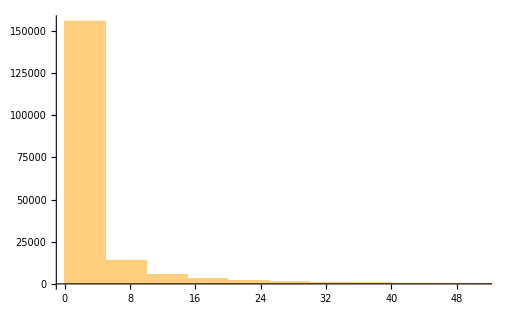

```mathematica
Histogram[Map[Length,eltbl["ci"]],{5}]
```

ノード:

```mathematica
(vltbl["ci"]=Table[VertexList[storyGrIdxFlDs3["ci"][[i]][[3]]],{i,Length[storyGrIdxFlDs3["ci"]]}])//Dimensions
```

{185893}

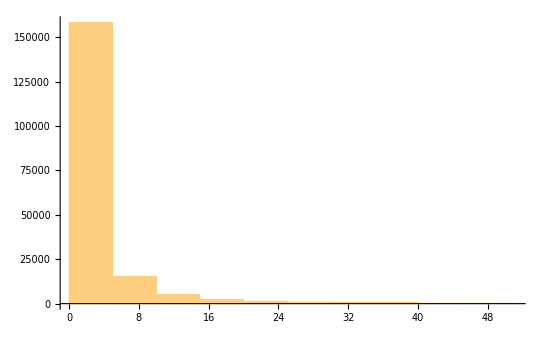

```mathematica
Histogram[Map[Length,vltbl["ci"]],{5}]
```

アクセス時刻:

```mathematica
(acct["ci"]=Map[#[[3,1]]&,eltbl["ci"],{2}])//Dimensions
```

{185893}

滞留時間：

```mathematica
(accspanMin["ci"]=Map[Max[#]-Min[#]&,acct["ci"]]/60)//Dimensions
```

{185893}

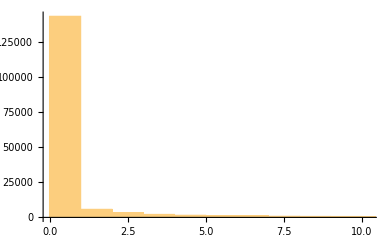

```mathematica
Histogram[accspanMin["ci"],{1}]
```

スタートノードが最小時刻になっていない。調整が必要か？

E/V ratio:

```mathematica
(ratioEV["ci"]=Map[Length,eltbl["ci"]]/Map[Length,vltbl["ci"]]//N)//Dimensions
```

{185893}

TV ratio :

```mathematica
(ratioTV["ci"]=acct["ci"]/Map[Length,vltbl["ci"]])//Dimensions
```

{185893}

TE ratio:

```mathematica
(ratioTE["ci"]=acct["ci"]/Map[Length,eltbl["ci"]])//Dimensions
```

{185893}

### Analysis 2 base interaction

リクエストパスから基盤名だけをとりだし、基盤連携を見る。

```mathematica
(GrBases["ci"]=Map[fqdnFromGraph[#[[3]]]&,storyGrIdxFlDs3["ci"]])//Dimensions
```

Part::partw: Part {1,3} of {cir.nii.ac.jp} does not exist.

StringJoin::string: String expected at position 1 in StringJoin[{cir.nii.ac.jp}⟦{1,3}⟧].

Part::partw: Part {1,3} of {} does not exist.

StringJoin::string: String expected at position 1 in StringJoin[{}⟦{1,3}⟧].

Part::partw: Part {1,3} of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

StringJoin::string: String expected at position 1 in StringJoin[{}⟦{1,3}⟧].

General::stop: Further output of StringJoin::string will be suppressed during this calculation.

{185893}

NII基盤(4基盤以外も)へのアクセスを見る。

```mathematica
niidnpos=Flatten[Position[Map[StringMatchQ[#,RegularExpression[".*nii.ac.jp.*"]]||StringMatchQ[#,RegularExpression[".*jdcat.jsps.go.jp.*"]]&,Flatten[GrBases["ci"]]//Union],True]]
```

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[StringJoin[{}⟦{1,3}⟧],RegularExpression[.*nii.ac.jp.*]].

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[StringJoin[{}⟦{1,3}⟧],RegularExpression[.*jdcat.jsps.go.jp.*]].

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[StringJoin[{cir.nii.ac.jp}⟦{1,3}⟧],RegularExpression[.*nii.ac.jp.*]].

General::stop: Further output of StringMatchQ::strse will be suppressed during this calculation.

{37,38,153,154,159,171,214,215,216,218,219,220,221,222,296,316,317,436,701,703,850,1093,1114,1115,1117,1168,1481,1589}

```mathematica
(Flatten[GrBases["ci"]]//Union)[[niidnpos]]
```

{http:ci.nii.ac.jp,http:cir.nii.ac.jp,https:alb-ci-nii-ac-jp-263480797.ap-northeast-1.elb.amazonaws.com,https:alb-ci-nii-ac-jp-263480797.ap-northeast-1.elb.amazonaws.com:443,https:api.ci.nii.ac.jp,https:auth.cir.nii.ac.jp,https:ci.nii.ac.jp,https:ci.nii.ac.jp:443,https:ci-nii-ac-jp.cdn.ampproject.org,https:cir.nii.ac.jp,https:cir-nii-ac-jp.bukkyo.idm.oclc.org,https:cir-nii-ac-jp.nanzan-u.idm.oclc.org,https:cir-nii-ac-jp.swu.idm.oclc.org,https:cir-nii-ac-jp.translate.goog,https:fukuoka-u.repo.nii.ac.jp,https:ge.nii.ac.jp,https:ge.nii.ac.jp:443,https:kaken.nii.ac.jp,https:niph.repo.nii.ac.jp,https:niu.repo.nii.ac.jp,https:rcos.nii.ac.jp,https:support.nii.ac.jp,https:tohoku.repo.nii.ac.jp,https:tohtech.repo.nii.ac.jp,https:tokoha-u.repo.nii.ac.jp,https:webfront2.nii.ac.jp:443,https:www.nii.ac.jp,https:www.unii.ac.jp}

```mathematica
(GrNiiBases["ci"]=Map[Cases[#,x_/;StringMatchQ[x,RegularExpression[".*nii.ac.jp.*"]]||StringMatchQ[x,RegularExpression[".*jdcat.jsps.go.jp.*"]]]&,GrBases["ci"]])//Dimensions
```

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[StringJoin[{cir.nii.ac.jp}⟦{1,3}⟧],RegularExpression[.*nii.ac.jp.*]].

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[StringJoin[{cir.nii.ac.jp}⟦{1,3}⟧],RegularExpression[.*jdcat.jsps.go.jp.*]].

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[StringJoin[{}⟦{1,3}⟧],RegularExpression[.*nii.ac.jp.*]].

General::stop: Further output of StringMatchQ::strse will be suppressed during this calculation.

{185893}

```mathematica
Map[Length,GrBases["ci"]]//Tally
```

{{2,163982},{1,21911}}

```mathematica
(GrBasesTly["ci"]=Tally[GrBases["ci"]])//Dimensions
```

{1733,2}

```mathematica
Map[Length,GrNiiBases["ci"]]//Tally
```

{{1,145383},{2,40510}}

```mathematica
(GrNiiBasesTly["ci"]=Tally[GrNiiBases["ci"]])//Dimensions
```

{28,2}

```mathematica
GrNiiBasesTly["ci"]//TableForm
```

https:cir.nii.ac.jp | 145383
https:ci.nii.ac.jp
https:cir.nii.ac.jp | 20274
http:ci.nii.ac.jp
https:cir.nii.ac.jp | 19934
https:cir.nii.ac.jp
https:support.nii.ac.jp | 127
https:cir.nii.ac.jp
https:www.nii.ac.jp | 5
https:ci.nii.ac.jp:443
https:cir.nii.ac.jp | 72
https:cir.nii.ac.jp
https:www.unii.ac.jp | 14
http:cir.nii.ac.jp
https:cir.nii.ac.jp | 46
https:cir.nii.ac.jp
https:kaken.nii.ac.jp | 5
https:cir.nii.ac.jp
https:rcos.nii.ac.jp | 4
https:cir.nii.ac.jp
https:fukuoka-u.repo.nii.ac.jp | 1
https:cir.nii.ac.jp
https:cir-nii-ac-jp.swu.idm.oclc.org | 3
https:cir.nii.ac.jp
https:cir-nii-ac-jp.nanzan-u.idm.oclc.org | 3
https:auth.cir.nii.ac.jp
https:cir.nii.ac.jp | 7
https:cir.nii.ac.jp
https:tohtech.repo.nii.ac.jp | 1
https:cir.nii.ac.jp
https:cir-nii-ac-jp.translate.goog | 2
https:cir.nii.ac.jp
https:tohoku.repo.nii.ac.jp | 1
https:cir.nii.ac.jp
https:cir-nii-ac-jp.bukkyo.idm.oclc.org | 1
https:cir.nii.ac.jp
https:niph.repo.nii.ac.jp | 1
https:alb-ci-nii-ac-jp-263480797.ap-northeast-1.elb.amazonaws.com:443
https:cir.nii.ac.jp | 1
https:alb-ci-nii-ac-jp-263480797.ap-northeast-1.elb.amazonaws.com
https:cir.nii.ac.jp | 1
https:ci-nii-ac-jp.cdn.ampproject.org
https:cir.nii.ac.jp | 1
https:cir.nii.ac.jp
https:ge.nii.ac.jp:443 | 1
https:cir.nii.ac.jp
https:tokoha-u.repo.nii.ac.jp | 1
https:api.ci.nii.ac.jp
https:cir.nii.ac.jp | 1
https:cir.nii.ac.jp
https:niu.repo.nii.ac.jp | 1
https:cir.nii.ac.jp
https:ge.nii.ac.jp | 1
https:cir.nii.ac.jp
https:webfront2.nii.ac.jp:443 | 1

グラフが多すぎるので選び方を考え中。

ここから、Idpで認証されたログはIdpがリファラーとして入ってくるが、認証元情報がはいらないため基盤連携のグラフに組み込まれない。
 一方で、Idpを遮蔽して認証元からアクセス先へのエッジは発生する。

### Analysis 3 time series

```mathematica
accessFirst=(Cases[accessTime["ci"],x_/;x>0]//Min)
```

3.90943×10^9

```mathematica
accessLast=(Cases[accessTime["ci"],x_/;x>0]//Max)
```

3.90951×10^9

```mathematica
Sort[accessTime["ci"]]//Length
```

2557038

```mathematica
BC600["ci"]=BinCounts[Sort[accessTime["ci"]],{accessFirst,accessLast,60*10}]
```

{15641,15400,14930,17957,17538,16736,16633,18048,17053,17045,19571,14858,17031,14912,12885,14700,14827,19503,17447,16164,14510,11866,10697,10259,12226,11674,12400,13942,11974,14300,11507,12327,11585,12235,13559,11868,9616,12919,14456,12646,14017,14760,13279,14891,11322,12413,14399,14230,12790,14020,12749,11245,11892,14435,14650,17372,16077,16478,15665,15796,14441,15398,16139,15649,17087,16308,16112,19271,19844,19842,19628,17004,15687,14906,14706,15601,17537,16595,17176,18400,17677,19190,21139,23122,20992,23251,21989,21082,24144,20845,20141,21648,24282,23536,24762,22934,20558,22629,23352,23309,24082,23870,23467,23131,20671,19542,21954,18599,17608,20921,22195,18824,20949,20980,19504,21505,19761,20354,21180,20752,20938,20587,19797,21318,20327,17673,18645,19109,19912,20250,20035,21223,21739,21954,20465,20884,20491,21812,20432,22276,22955,22605,22735}

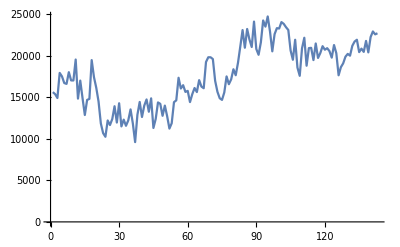

```mathematica
ListPlot[BC600["ci"],PlotRange->Full,Joined->True]
```

### Analysis 4 CKAN impact

ckanCRIDを含むグラフを抽出する。

すでに構成したハッシュとグラフのプロパティを当てる関数。ひとつでもあたればTrueを返す。
 ハッシュはログ中の位置を記述しており、リクエストパス・リファラーを分けたもの、Unionしたもの。

滞留時間をグラフから得る関数：

```mathematica
stayTime[g_Graph]:=Module[{elist,tlist},
elist=EdgeList[g];
tlist=Map[#[[3,1]]&,elist];
Max[tlist]-Min[tlist]
]
```

ckanCRIDを含むログの行とグラフのエッジにあるログの行を当てる関数 （T/F）:

```mathematica
logGraphQ[gr_Graph,asc_Association]:=Module[{elist,logposlist,res},
elist=EdgeList[gr];
logposlist=Map[#[[3,2]]&,elist];
res=Map[asc[#]&,logposlist];
Position[res,_Integer,{1}]/.{{}->False,{__}->True}
]
```

ckanCRIDをリクエストに含むノードをハイライトする関数：

```mathematica
ckanVertexHighlihgt[g_Graph,asc_Association]:=Module[{vlist,pos,targetv,op},
vlist=VertexList[g];
pos=Flatten[Position[Map[ckanCridPRACQ[toCRID[#]]&,VertexList[g]],True]];
targetv=vlist[[pos]];
op=VertexStyle->Map[#->Red&,targetv];
Graph[g,op]
]
```

CKAN - CRIDを含むグラフの抽出

```mathematica
(ckanGrP["ci"]=Map[If[logGraphQ[#[[3]],ckanCridPLogPosAC["ci"]],#,Null]&,storyGrIdxFlDs3["ci"]])//Dimensions
```

{185893}

```mathematica
(ckanGrR["ci"]=Map[If[logGraphQ[#[[3]],ckanCridRLogPosAC["ci"]],#,Null]&,storyGrIdxFlDs3["ci"]])//Dimensions
```

{185893}

```mathematica
(ckanGrPR["ci"]=Map[If[logGraphQ[#[[3]],ckanCridPRLogPosAC["ci"]],#,Null]&,storyGrIdxFlDs3["ci"]])//Dimensions
```

{185893}

```mathematica
(ckanGrPsel["ci"]=Cases[ckanGrP["ci"],{__},{1}])//Dimensions
```

{99,3}

```mathematica
ckanGrPselVL["ci"]=Map[VertexList[#[[3]]]&,ckanGrPsel["ci"]];
```

```mathematica
ckanGrPselEL["ci"]=Map[EdgeList[#[[3]]]&,ckanGrPsel["ci"]];
```

```mathematica
(ckanGrRsel["ci"]=Cases[ckanGrR["ci"],{__},{1}])//Dimensions
```

{17,3}

```mathematica
ckanGrRselVL["ci"]=Map[VertexList[#[[3]]]&,ckanGrRsel["ci"]];
```

```mathematica
ckanGrRselEL["ci"]=Map[EdgeList[#[[3]]]&,ckanGrRsel["ci"]];
```

```mathematica
(ckanGrPRsel["ci"]=Cases[ckanGrPR["ci"],{__},{1}])//Dimensions
```

{101,3}

```mathematica
ckanGrPRselVL["ci"]=Map[VertexList[#[[3]]]&,ckanGrPRsel["ci"]];
```

```mathematica
ckanGrPRselEL["ci"]=Map[EdgeList[#[[3]]]&,ckanGrPRsel["ci"]];
```

```mathematica
(ckanGrPRselHL["ci"]=Map[{#[[1]],#[[2]],ckanVertexHighlihgt[#[[3]],ckanCridPRACQ]}&,ckanGrPRsel["ci"]])//Dimensions
```

{101,3}

```mathematica
ckanGrPRVcount["ci"]=Map[VertexCount[#[[3]]]&,ckanGrPRselHL["ci"]]
```

{2,8,14,2,5,14,34,2,2,2,2,2,93,92,93,37,21,43,105,14,9,2,13,26,10,20,2,19,35,269,265,265,41,46,67,6,31,18,18,25,11,12,12,6,8,13,26,14,14,17,45,2,27,41,45,7,22,12,14,16,24,8,18,68,72,69,65,423,423,462,423,423,426,423,11,17,94,99,95,62,14,2,23,4,2,25,6,29,16,23,36,36,36,9,7,18,11,3,6,1099,17}

```mathematica
accTimeList[g_Graph]:=Module[{elist,tlist},
elist=EdgeList[g];
tlist=Sort[Map[#[[3,1]]&,elist],#1>#2&]
]
```

```mathematica
timeSpan[tlist_]:=Map[(#[[1]]-#[[2]])&,Partition[tlist,2,1]]
```

```mathematica
ckanGrPRstayTime["ci"]=Map[stayTime[#[[3]]]&,ckanGrPRselHL["ci"]]
```

{0.,181.,236.,0.,62.,10090.,29306.,0.,0.,0.,0.,0.,19258.,19246.,19246.,2084.,16014.,4963.,35597.,1652.,779.,0.,1471.,1522.,7197.,3292.,0.,3870.,3960.,12997.,3326.,3326.,17575.,29621.,30254.,38.,28696.,8609.,8648.,5124.,2778.,698.,145.,154.,218.,13946.,14936.,13946.,746.,547.,80409.,0.,27159.,14603.,5688.,103.,15398.,1778.,2091.,11978.,13402.,17069.,12300.,18443.,28412.,22531.,18443.,33342.,33342.,41975.,33342.,34501.,33342.,33342.,1610.,13257.,26838.,26826.,26826.,4057.,1811.,0.,6275.,22.,0.,12197.,10232.,3259.,7351.,736.,1259.,1222.,1222.,196.,177.,620.,1537.,5.,25958.,86309.,1379.}

### Analysis 5 CKAN graph reform

program :

可能な全Vertexにアクセス時間リストを付与：

```mathematica
gatherDistributeUniq[l_]:=Module[{first,target},
first=l[[1,1]];
target=Map[#[[2]]&,l];
{first,target}
]
```

```mathematica
gatherDistributeUniqRl[l_]:=Module[{first,target},
first=l[[1,1]];
target=Map[#[[2]]&,l];
first->{first,target}
]
```

```mathematica
addVertexAccTime[g_]:=Module[{gatherTimeV,gatherTimeVRl},
gatherTimeV=Gather[Map[{#[[2]],#[[3,1]]}&,EdgeList[g]],#1[[1]]==#2[[1]]&];
gatherTimeVRl=Map[gatherDistributeUniqRl,gatherTimeV];
VertexReplace[g,gatherTimeVRl]
]
```

```mathematica
guessVertexCoorGr[g_,timeshift_]:=Module[{allAccTime,baseTime,repPos,target,repRl},
allAccTime=Cases[Flatten[Map[#[[2]]&,g//VertexList]],_Real];
baseTime=Min[allAccTime]+timeshift;
repPos=Flatten[Position[Map[Head,VertexList[g]],String]];
target=Map[VertexList[g][[#]]&,repPos];
repRl=Map[#->{#,{baseTime}}&,target];
VertexReplace[g,repRl]
]
```

```mathematica
accTimeMinGr[g_]:=Min[Cases[Flatten[Map[#[[2]]&,g//VertexList]],_Real]]
```

```mathematica
reformCoorGr[g_,baseTime_,f_]:=f[Map[{Max[#[[2]]],Min[#[[2]]]}&,VertexList[g]]-baseTime]
```

```mathematica
timeLineGr[g_,timeshift_,f_]:=Module[{gnew,btime,coornew},
gnew=guessVertexCoorGr[g,timeshift];
btime=accTimeMinGr[gnew];
coornew=reformCoorGr[gnew,btime,f];
Graph[gnew,VertexSize->Automatic,VertexCoordinates->coornew]
]
```

```mathematica
(ckanGrPRselHLAT["ci"]=Map[{#[[1]],#[[2]],addVertexAccTime[#[[3]]]}&,ckanGrPRselHL["ci"]])//Dimensions
```

{101,3}

ロググループ：

```mathematica
loggroupCKAN=Map[#[[2]]&,ckanGrPRselHLAT["ci"]]
```

{{1566,1},{7079,1},{8551,1},{11047,1},{15020,1},{19348,1},{19502,1},{21347,1},{21353,1},{21450,1},{21666,1},{28703,1},{28959,1},{28959,1},{28959,1},{29086,1},{29207,1},{29961,1},{33524,1},{36561,1},{37561,1},{42385,1},{43857,1},{48528,1},{49133,1},{49696,1},{51229,1},{51662,1},{56808,1},{59750,1},{59750,1},{59750,1},{62818,1},{63093,1},{63093,1},{64114,1},{64463,1},{64463,1},{64463,1},{72066,1},{72427,1},{74511,1},{75873,1},{81833,1},{84884,1},{84918,1},{84918,1},{84918,1},{94290,1},{98904,1},{99367,1},{101580,1},{101803,1},{101885,1},{101885,1},{103505,1},{104051,1},{104359,1},{104359,1},{104360,1},{104360,1},{104364,1},{104540,1},{105308,1},{105308,1},{105308,1},{105308,1},{105469,1},{105469,1},{105469,1},{105469,1},{105469,1},{105469,1},{105469,1},{105631,1},{105807,1},{105846,1},{105846,1},{105846,1},{107306,1},{109955,1},{110630,1},{111631,1},{111924,1},{113106,1},{114645,1},{118235,1},{118899,1},{118926,1},{120276,1},{121169,1},{121169,1},{121169,1},{124072,1},{126689,1},{137992,1},{140745,1},{144916,1},{153474,1},{157773,1},{161796,1}}

ノードの数え上げ：

```mathematica
vcCKAN=Map[VertexCount[#[[3]]]&,ckanGrPRselHLAT["ci"]]
```

{2,8,14,2,5,14,34,2,2,2,2,2,93,92,93,37,21,43,105,14,9,2,13,26,10,20,2,19,35,269,265,265,41,46,67,6,31,18,18,25,11,12,12,6,8,13,26,14,14,17,45,2,27,41,45,7,22,12,14,16,24,8,18,68,72,69,65,423,423,462,423,423,426,423,11,17,94,99,95,62,14,2,23,4,2,25,6,29,16,23,36,36,36,9,7,18,11,3,6,1099,17}

エッジの数え上げ：

```mathematica
ecCKAN=Map[EdgeCount[#[[3]]]&,ckanGrPRselHLAT["ci"]]
```

{1,14,28,1,5,15,59,1,1,1,1,1,153,140,150,55,42,63,148,15,12,1,17,52,13,42,1,32,75,667,512,513,56,83,111,5,43,22,23,29,13,14,19,6,8,15,34,16,17,23,68,1,37,76,81,12,30,13,16,25,40,9,22,92,108,98,94,650,652,743,652,656,657,652,26,45,265,269,267,100,20,1,27,4,1,64,5,87,18,35,50,48,49,14,7,37,15,2,5,1373,22}

アクセス時刻：

```mathematica
(accCKAN=Map[Map[#[[3,1]]&,EdgeList[#[[3]]]]&,ckanGrPRselHLAT["ci"]])//Dimensions
```

{101}

最大滞在時間：

```mathematica
maxTimeSpan[l_]:=Max[Map[#[[1]]-#[[2]]&,Partition[Sort[l,#1>#2&],2,1]]]
```

```mathematica
(maxtimespanCKAN=Map[maxTimeSpan,accCKAN]/.{-Infinity->0})/60
```

{0,0.716667,1.03333,0,0.433333,86.7333,464.733,0,0,0,0,0,64.7833,72.8333,72.8333,11.2833,243.067,67.05,351.3,7.96667,7.68333,0,15.95,16.8,73.05,19.5833,0,21.1167,37.7833,107.017,7.48333,7.48333,151.6,273.583,344.167,0.3,171.733,128.767,128.767,37.0667,37.55,8.03333,0.416667,2.05,1.78333,228.283,175.817,227.85,4.78333,6.01667,1107.65,0,160.133,139.1,54.85,0.65,157.65,26.65,26.4667,99.0333,98.8167,280.433,192.583,88.9167,107.2,168.25,168.25,67.6,67.6,94.25,67.6,67.6,67.6,67.6,11.4667,100.233,118.8,118.8,118.717,10.8667,6.05,0,89.9167,0.2,0,120.667,134.833,7.85,61.5333,2.63333,4.81667,4.81667,4.81667,2.15,1.06667,2.08333,15.2667,0.0833333,240.6,26.95,13.7667}

滞留時間：

```mathematica
staytimeCKAN=Map[Max[#]-Min[#]&,accCKAN]
```

{0.,181.,236.,0.,62.,10090.,29306.,0.,0.,0.,0.,0.,19258.,19246.,19246.,2084.,16014.,4963.,35597.,1652.,779.,0.,1471.,1522.,7197.,3292.,0.,3870.,3960.,12997.,3326.,3326.,17575.,29621.,30254.,38.,28696.,8609.,8648.,5124.,2778.,698.,145.,154.,218.,13946.,14936.,13946.,746.,547.,80409.,0.,27159.,14603.,5688.,103.,15398.,1778.,2091.,11978.,13402.,17069.,12300.,18443.,28412.,22531.,18443.,33342.,33342.,41975.,33342.,34501.,33342.,33342.,1610.,13257.,26838.,26826.,26826.,4057.,1811.,0.,6275.,22.,0.,12197.,10232.,3259.,7351.,736.,1259.,1222.,1222.,196.,177.,620.,1537.,5.,25958.,86309.,1379.}

```mathematica
staytimeCKAN/60
```

{0.,3.01667,3.93333,0.,1.03333,168.167,488.433,0.,0.,0.,0.,0.,320.967,320.767,320.767,34.7333,266.9,82.7167,593.283,27.5333,12.9833,0.,24.5167,25.3667,119.95,54.8667,0.,64.5,66.,216.617,55.4333,55.4333,292.917,493.683,504.233,0.633333,478.267,143.483,144.133,85.4,46.3,11.6333,2.41667,2.56667,3.63333,232.433,248.933,232.433,12.4333,9.11667,1340.15,0.,452.65,243.383,94.8,1.71667,256.633,29.6333,34.85,199.633,223.367,284.483,205.,307.383,473.533,375.517,307.383,555.7,555.7,699.583,555.7,575.017,555.7,555.7,26.8333,220.95,447.3,447.1,447.1,67.6167,30.1833,0.,104.583,0.366667,0.,203.283,170.533,54.3167,122.517,12.2667,20.9833,20.3667,20.3667,3.26667,2.95,10.3333,25.6167,0.0833333,432.633,1438.48,22.9833}

```mathematica
f[x_]=Log[x+1]
```

Log[1+x]

```mathematica
(ckanGrPRselHLTL["ci"]=Map[timeLineGr[#[[3]],-60,f]&,ckanGrPRselHLAT["ci"]])//Dimensions
```

Part::partd: Part specification https://www.google.com/⟦2⟧ is longer than depth of object.

Part::partd: Part specification https://www.google.com/url?q=https://cir.nii.ac.jp/&sa=U&sqi=2&ved=2ahUKEwihwqOM0dGCAxVGNN4KHW73BGMQFnoECAcQAQ&usg=AOvVaw1TP0cPw4owrZdTH0aWcRIf⟦2⟧ is longer than depth of object.

Part::partd: Part specification https://www.google.com/url?q=https://cir.nii.ac.jp/&sa=U&sqi=2&ved=2ahUKEwiaq_TUkNKCAxUPsFYBHRnID74QFnoECAUQAQ&usg=AOvVaw3bwiI2wZC5Md_ZZTpkmgcf⟦2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

{101}

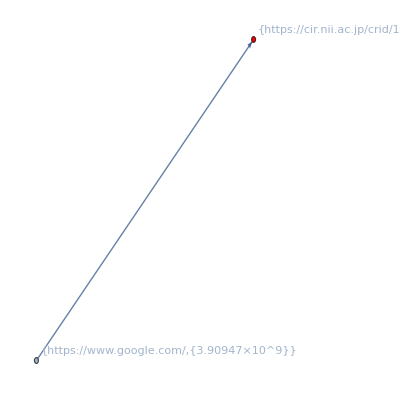
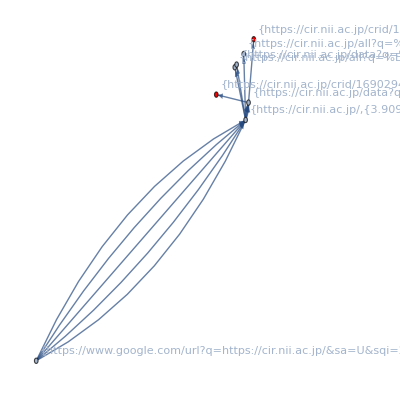
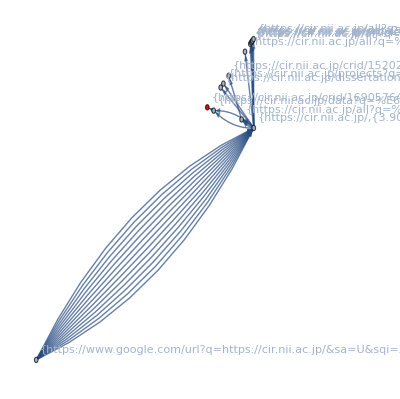
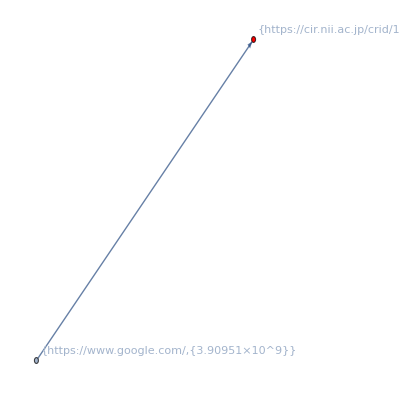
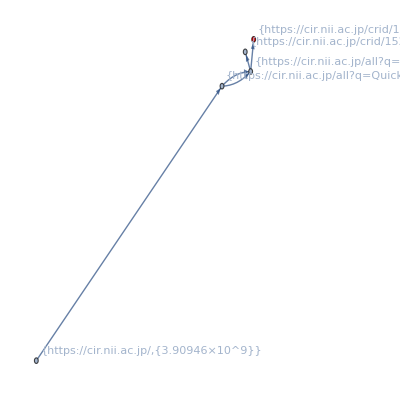
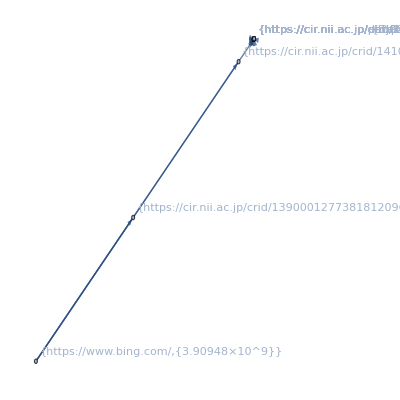
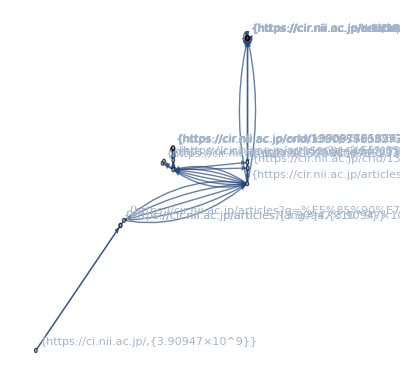
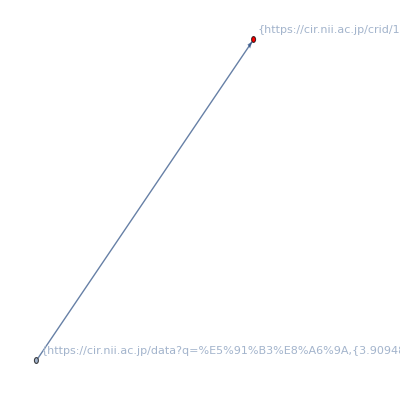
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-

```mathematica
ckanGrPRselHLTL["ci"]//TableForm
```

### Analysis 6 CKAN voc-graph

vocRlの読み込み：

```mathematica
vocRlFiles=FileNames[vocdir<>"/*.wl"]
```

{/Volumes/home/NII/togo-log/rcoslogs/voc/voc_path_action_ci_rl.wl,/Volumes/home/NII/togo-log/rcoslogs/voc/voc_path_action_cs_rl.wl,/Volumes/home/NII/togo-log/rcoslogs/voc/voc_path_action_la_rl.wl,/Volumes/home/NII/togo-log/rcoslogs/voc/voc_path_action_wk_rl.wl,/Volumes/home/NII/togo-log/rcoslogs/voc/voc_ref_action_ci_rl.wl,/Volumes/home/NII/togo-log/rcoslogs/voc/voc_ref_action_cs_rl.wl,/Volumes/home/NII/togo-log/rcoslogs/voc/voc_ref_action_la_rl.wl,/Volumes/home/NII/togo-log/rcoslogs/voc/voc_ref_action_wk_rl.wl}

```mathematica
vocRlList=Map[Get,vocRlFiles];
```

```mathematica
(vocRl["all:path"]=Apply[Join,vocRlList])//Dimensions
```

{113}

```mathematica
vocRl["all:path"][[1]]
```

x_/;StringMatchQ[x,RegularExpression[https://cir.nii.ac.jp/]]→voc[ci:top]

===== /プログラム検討 =====

====== /引数 ======

====== 引数/ ======

====== /内部変数 ======

====== 内部変数/ ======

===== プログラム検討/ =====

```mathematica
toVocGraph[gr_,rl_]:=Module[{vl,vname,vrename,vrenameRl},
Print["it may cause StringMatchQ warn."];
vl=VertexList[gr];
vname=Map[#[[1]]&,vl];
vrename=(vname/.rl);
vrenameRl=Map[Apply[Rule,#]&,Transpose[{vl,vrename}]];
Graph[gr,VertexLabels->vrenameRl]
]
```

it may cause StringMatchQ warn.

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[List,RegularExpression[https://cir.nii.ac.jp/]].

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[List,RegularExpression[https://cir.nii.ac.jp/ja]].

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[List,RegularExpression[https://cir.nii.ac.jp/\?.*]].

General::stop: Further output of StringMatchQ::strse will be suppressed during this calculation.

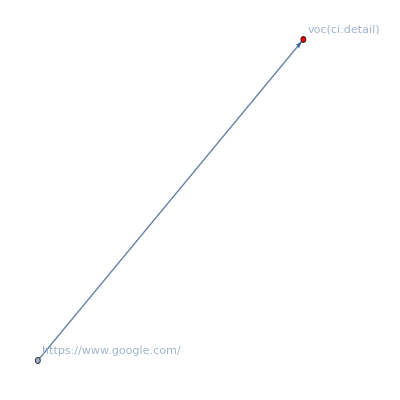

```mathematica
toVocGraph[ckanGrPRselHLTL["ci"][[1]],vocRl["all:path"]]
```

it may cause StringMatchQ warn.

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[List,RegularExpression[https://cir.nii.ac.jp/]].

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[List,RegularExpression[https://cir.nii.ac.jp/ja]].

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[List,RegularExpression[https://cir.nii.ac.jp/\?.*]].

General::stop: Further output of StringMatchQ::strse will be suppressed during this calculation.

it may cause StringMatchQ warn.

it may cause StringMatchQ warn.

it may cause StringMatchQ warn.

«97 more identical outputs»

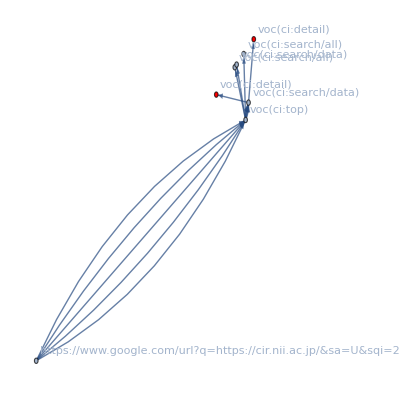
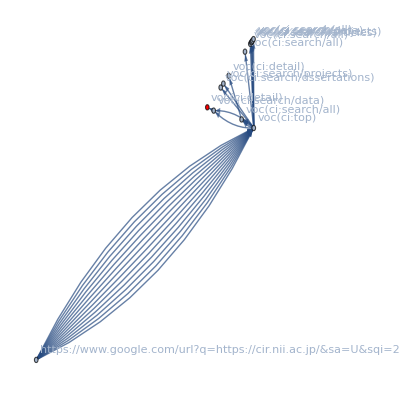
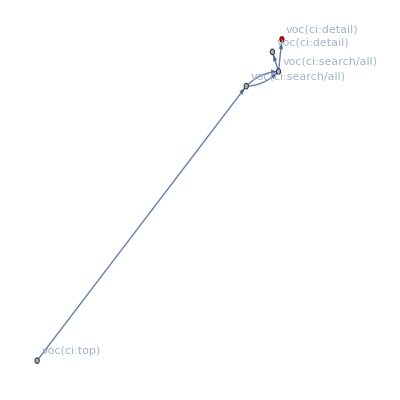
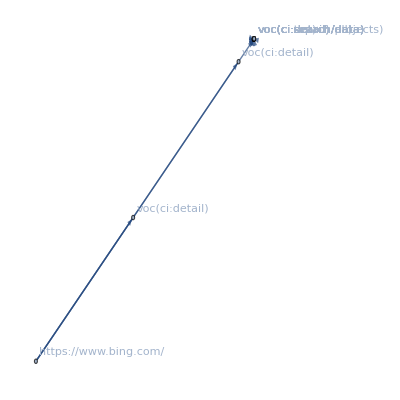
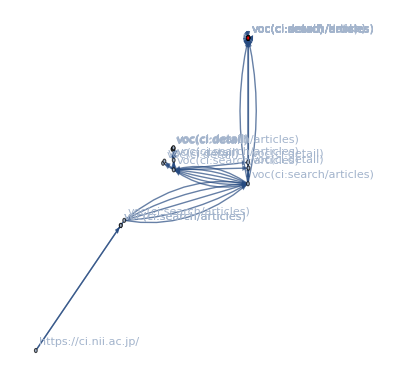
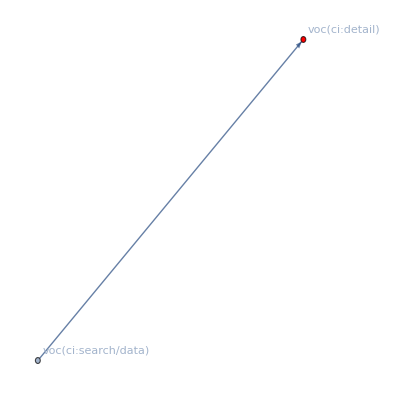
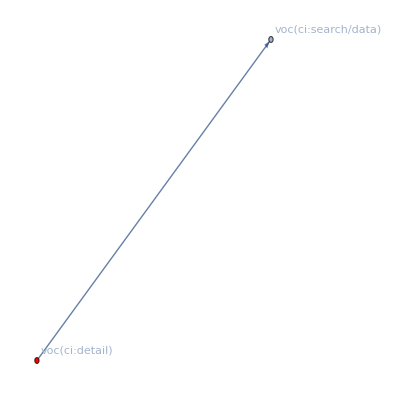
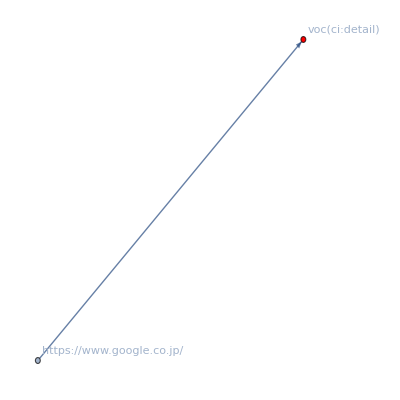
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-

```mathematica
Map[toVocGraph[#,vocRl["all:path"]]&,ckanGrPRselHLTL["ci"]]//TableForm
```

### Report:CKAN impact

```mathematica
(logTotal={{"- ログ件数 -","述べログ件数"},{"全件数",ToExpression[StringSplit[logwc][[1]]]},{"ユーザーアクセス件数",idxLogLen["ci"]}})//TableForm
```

- ログ件数 - | 述べログ件数
全件数 | 22645372
ユーザーアクセス件数 | 2557038

```mathematica
(ckanLogTotal={{"- CKAN-cridを含むログ件数 -","述べログ件数","cridのユニーク件数"},
{"リクエストにCKAN-crid含む",ckanCridPLogPos["ci"]//Length,Union[ckanCridPlist]//Length},
{"リファラーにCKAN-crid含む",ckanCridRLogPos["ci"]//Length,Union[ckanCridRlist]//Length},
{"いずれか含む",ckanCridPRLogPos["ci"]//Length,ckanCridPRU//Length}
})//TableForm
```

- CKAN-cridを含むログ件数 - | 述べログ件数 | cridのユニーク件数
リクエストにCKAN-crid含む | 188 | 159
リファラーにCKAN-crid含む | 25 | 14
いずれか含む | 213 | 159

```mathematica
(ckanChainTotal={{"- アクション連鎖数 -","件数"},
{"全件数",storyGrIdxFlDs3["ci"]//Length},
{"ノードにCKAN-crid含む",ckanGrPRselHL["ci"]//Length}
})//TableForm
```

- アクション連鎖数 - | 件数
全件数 | 185893
ノードにCKAN-crid含む | 101

```mathematica
(ckanGraphSummary=Prepend[Transpose[{Table[i,{i,Length[loggroupCKAN]}],loggroupCKAN,vcCKAN,ecCKAN,maxtimespanCKAN/60,staytimeCKAN/60}],{"アクセスグラフ通し番号","ロググループ","ノード数","エッジ数","最大滞在時間(分)","滞留時間(分)"}])//TableForm
```

アクセスグラフ通し番号 | ロググループ | ノード数 | エッジ数 | 最大滞在時間(分) | 滞留時間(分)
1 | 1566
1 | 2 | 1 | 0 | 0.
2 | 7079
1 | 8 | 14 | 0.716667 | 3.01667
3 | 8551
1 | 14 | 28 | 1.03333 | 3.93333
4 | 11047
1 | 2 | 1 | 0 | 0.
5 | 15020
1 | 5 | 5 | 0.433333 | 1.03333
6 | 19348
1 | 14 | 15 | 86.7333 | 168.167
7 | 19502
1 | 34 | 59 | 464.733 | 488.433
8 | 21347
1 | 2 | 1 | 0 | 0.
9 | 21353
1 | 2 | 1 | 0 | 0.
10 | 21450
1 | 2 | 1 | 0 | 0.
11 | 21666
1 | 2 | 1 | 0 | 0.
12 | 28703
1 | 2 | 1 | 0 | 0.
13 | 28959
1 | 93 | 153 | 64.7833 | 320.967
14 | 28959
1 | 92 | 140 | 72.8333 | 320.767
15 | 28959
1 | 93 | 150 | 72.8333 | 320.767
16 | 29086
1 | 37 | 55 | 11.2833 | 34.7333
17 | 29207
1 | 21 | 42 | 243.067 | 266.9
18 | 29961
1 | 43 | 63 | 67.05 | 82.7167
19 | 33524
1 | 105 | 148 | 351.3 | 593.283
20 | 36561
1 | 14 | 15 | 7.96667 | 27.5333
21 | 37561
1 | 9 | 12 | 7.68333 | 12.9833
22 | 42385
1 | 2 | 1 | 0 | 0.
23 | 43857
1 | 13 | 17 | 15.95 | 24.5167
24 | 48528
1 | 26 | 52 | 16.8 | 25.3667
25 | 49133
1 | 10 | 13 | 73.05 | 119.95
26 | 49696
1 | 20 | 42 | 19.5833 | 54.8667
27 | 51229
1 | 2 | 1 | 0 | 0.
28 | 51662
1 | 19 | 32 | 21.1167 | 64.5
29 | 56808
1 | 35 | 75 | 37.7833 | 66.
30 | 59750
1 | 269 | 667 | 107.017 | 216.617
31 | 59750
1 | 265 | 512 | 7.48333 | 55.4333
32 | 59750
1 | 265 | 513 | 7.48333 | 55.4333
33 | 62818
1 | 41 | 56 | 151.6 | 292.917
34 | 63093
1 | 46 | 83 | 273.583 | 493.683
35 | 63093
1 | 67 | 111 | 344.167 | 504.233
36 | 64114
1 | 6 | 5 | 0.3 | 0.633333
37 | 64463
1 | 31 | 43 | 171.733 | 478.267
38 | 64463
1 | 18 | 22 | 128.767 | 143.483
39 | 64463
1 | 18 | 23 | 128.767 | 144.133
40 | 72066
1 | 25 | 29 | 37.0667 | 85.4
41 | 72427
1 | 11 | 13 | 37.55 | 46.3
42 | 74511
1 | 12 | 14 | 8.03333 | 11.6333
43 | 75873
1 | 12 | 19 | 0.416667 | 2.41667
44 | 81833
1 | 6 | 6 | 2.05 | 2.56667
45 | 84884
1 | 8 | 8 | 1.78333 | 3.63333
46 | 84918
1 | 13 | 15 | 228.283 | 232.433
47 | 84918
1 | 26 | 34 | 175.817 | 248.933
48 | 84918
1 | 14 | 16 | 227.85 | 232.433
49 | 94290
1 | 14 | 17 | 4.78333 | 12.4333
50 | 98904
1 | 17 | 23 | 6.01667 | 9.11667
51 | 99367
1 | 45 | 68 | 1107.65 | 1340.15
52 | 101580
1 | 2 | 1 | 0 | 0.
53 | 101803
1 | 27 | 37 | 160.133 | 452.65
54 | 101885
1 | 41 | 76 | 139.1 | 243.383
55 | 101885
1 | 45 | 81 | 54.85 | 94.8
56 | 103505
1 | 7 | 12 | 0.65 | 1.71667
57 | 104051
1 | 22 | 30 | 157.65 | 256.633
58 | 104359
1 | 12 | 13 | 26.65 | 29.6333
59 | 104359
1 | 14 | 16 | 26.4667 | 34.85
60 | 104360
1 | 16 | 25 | 99.0333 | 199.633
61 | 104360
1 | 24 | 40 | 98.8167 | 223.367
62 | 104364
1 | 8 | 9 | 280.433 | 284.483
63 | 104540
1 | 18 | 22 | 192.583 | 205.
64 | 105308
1 | 68 | 92 | 88.9167 | 307.383
65 | 105308
1 | 72 | 108 | 107.2 | 473.533
66 | 105308
1 | 69 | 98 | 168.25 | 375.517
67 | 105308
1 | 65 | 94 | 168.25 | 307.383
68 | 105469
1 | 423 | 650 | 67.6 | 555.7
69 | 105469
1 | 423 | 652 | 67.6 | 555.7
70 | 105469
1 | 462 | 743 | 94.25 | 699.583
71 | 105469
1 | 423 | 652 | 67.6 | 555.7
72 | 105469
1 | 423 | 656 | 67.6 | 575.017
73 | 105469
1 | 426 | 657 | 67.6 | 555.7
74 | 105469
1 | 423 | 652 | 67.6 | 555.7
75 | 105631
1 | 11 | 26 | 11.4667 | 26.8333
76 | 105807
1 | 17 | 45 | 100.233 | 220.95
77 | 105846
1 | 94 | 265 | 118.8 | 447.3
78 | 105846
1 | 99 | 269 | 118.8 | 447.1
79 | 105846
1 | 95 | 267 | 118.717 | 447.1
80 | 107306
1 | 62 | 100 | 10.8667 | 67.6167
81 | 109955
1 | 14 | 20 | 6.05 | 30.1833
82 | 110630
1 | 2 | 1 | 0 | 0.
83 | 111631
1 | 23 | 27 | 89.9167 | 104.583
84 | 111924
1 | 4 | 4 | 0.2 | 0.366667
85 | 113106
1 | 2 | 1 | 0 | 0.
86 | 114645
1 | 25 | 64 | 120.667 | 203.283
87 | 118235
1 | 6 | 5 | 134.833 | 170.533
88 | 118899
1 | 29 | 87 | 7.85 | 54.3167
89 | 118926
1 | 16 | 18 | 61.5333 | 122.517
90 | 120276
1 | 23 | 35 | 2.63333 | 12.2667
91 | 121169
1 | 36 | 50 | 4.81667 | 20.9833
92 | 121169
1 | 36 | 48 | 4.81667 | 20.3667
93 | 121169
1 | 36 | 49 | 4.81667 | 20.3667
94 | 124072
1 | 9 | 14 | 2.15 | 3.26667
95 | 126689
1 | 7 | 7 | 1.06667 | 2.95
96 | 137992
1 | 18 | 37 | 2.08333 | 10.3333
97 | 140745
1 | 11 | 15 | 15.2667 | 25.6167
98 | 144916
1 | 3 | 2 | 0.0833333 | 0.0833333
99 | 153474
1 | 6 | 5 | 240.6 | 432.633
100 | 157773
1 | 1099 | 1373 | 26.95 | 1438.48
101 | 161796
1 | 17 | 22 | 13.7667 | 22.9833

### Export:CKAN impact

エッジリスト：

```mathematica
(ckanEL=Map[MapApply[List,EdgeList[#]]&,ckanGrPRselHLTL["ci"]])//Dimensions
```

{101}

```mathematica
ckanELexp=Map[{#[[1,1]],#[[2,1]]}&,ckanEL,{2}];
```

```mathematica
expdir=mountdir<>"log/D="<>date<>"/"<>base["ci"]
```

/Volumes/home/NII/togo-log/rcoslogs/log/D=20231120/T=ci

```mathematica
SetDirectory[expdir]
```

/Volumes/home/NII/togo-log/rcoslogs/log/D=20231120/T=ci

```mathematica
Export["ckanedgelist.json",ckanELexp]
```

ckanedgelist.json

ログ件数、ckanグラフまとめ：

```mathematica
Export["graphProperty.xlsx",{logTotal,ckanLogTotal,ckanChainTotal,ckanGraphSummary}]
```

graphProperty.xlsx

## 終端処理

```mathematica
end=AbsoluteTime[Date[]]
```

3.910268226245874×10^9

```mathematica
end-start
```

783.724591